# Getting Start with AI

## Kareem Ahmed Yi Yin Wolfram Research

-Graphics-	-Graphics-

## Wolfram Language Syntax basics

All commands, functions, data, etc. can be entered like this...

Head[argument1, argument2 ...]

The Head.

The head describes what the function does (eg Classify) or what the data represents (e.g. Image). All the words are capitalised, a format called CamelCase.

Square brackets.

Comma separated arguments.

Data is grouped together with braces { } e.g. {1,2,3,...} or for x-y pairs {{1,2},{2,4},{3,5},...}

Key-value data is grouped with an arrow → typed with minus and greater eg. “Name”->”Jon”

The final part of an expression is how to evaluate it!  You must press ⇧⌤ to evaluate the cell.

## Machine Learning?

### Computer “Learns” a Model from Data

model = program with tunable parameters

learning = tuning parameters to fit data

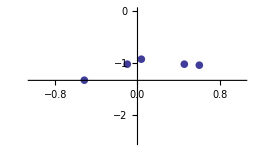
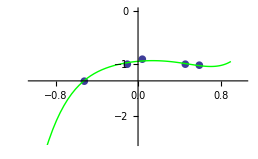
-Graphics-	⟶	-Graphics-

{ →cat, →dog,...}	⟶	-Graphics-

### Typical Tasks

Classification of images, sound, text, etc.

→cat, →dog,...

Prediction of a variable in a dataset

(6 yo, female) → 1.15 m, (11 yo, male) → 1.48 m, ...

Text translation

“the house is blue” → “la maison est bleue”

Prediction of a time series

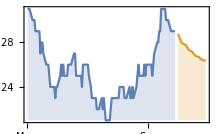

Anomaly detection

-Graphics-

Data clustering

-Graphics-

Robot learning how to walk

### Learning Paradigms

Supervised learning

Input → output mapping from examples

Most common paradigm

Unsupervised learning

Only inputs

On the rise

Reinforcement learning

Active agent, feedback from environment

Not much used yet (but a lot of research)

## In the Wolfram Language

### Automatic Machine Learning Framework

Functions:

Classify & Predict

ClusterClassify, FindClusters, etc.

DimensionReduction, FeatureExtraction

FindDistribution, FindFormula

Very easy to use

Task oriented

Automatic

Wide range of data types (numerical, images, text, etc.)

### Neural Network Framework

Model oriented

High flexibility

High performance

GPU training

Out-of-core training

```mathematica
NetGraph[{Ramp,LogisticSigmoid,CatenateLayer[]},{1->2,{1,2}->3}]
```

NetGraph[]

### Developed Using Machine Learning

Built-in classifiers, ImageIdentify, TextCases, etc.

## Built-in Machine Learning

### Built-in Classifiers

```mathematica
cl=Classify["Language"]
```

ClassifierFunction[…]

```mathematica
cl["Quelle est cette langue?"]
```

French

```mathematica
cl["What is this language?","TopProbabilities"]
```

{English→0.999976}

### ImageIdentify

```mathematica
ImageIdentify[-Graphics-]
```

gray wolf

```mathematica
ImageIdentify[-Graphics-]
```

key lime

### TextStructure

```mathematica
str=TextStructure["The house is blue. My dog is fast."]
```

The
Determinerhouse
Noun
Noun Phrase  is
Verb  blue
Adjective
Adjective Phrase
Verb Phrase.
Punctuation
Sentence
    My
Pronoundog
Noun
Noun Phrase  is
Verb  fast
Adjective
Adjective Phrase
Verb Phrase.
Punctuation
Sentence

### TextCases

```mathematica
moon=WikipediaData["Moon"];
```

```mathematica
TextCases[moon,"Quantity"->"Interpretation"]
```

{400 km,900 mi,28 in,8 in,380 kg,840 lb,500 km,737 km,240 km,150 mi,300 km,190 mi,500 km,310 mi,50 km,31 mi,350 km,220 mi,240 km,390 mi,13 km,1 mi,9 km,2 mi,300 ft,1 km,6 mi,20 km,4 mi,5 km,1 mi,1960 s,400 sq,0 ppm,300 kg,100 lb,100 kg,220 lb,12 kg,26 lb,1410 ppm,15 atm,3 nPa,35 K,26 K,700 km,100 mi,400 km,500 mi,700 km,700 mi,3 km,9 mi,38 mm,5 in,10 cm,4 in,428 BC,37 BC,322 BC,212 BC,1870 s,1940 s,1950 s,16 in,20 in,24 in,3 kg,1973 as,1950 s,87 lb,1960 s,1980 s,1990 s,24 in,2 in,40 km,25 mi,5 km,2 mi}

```mathematica
TakeLargest[Counts[TextCases[moon,"Noun"]],10]
```

<|surface→42,moon→30,water→29,impact→27,years→26,lunar→26,mission→25,side→24,orbit→21,spacecraft→20|>

```mathematica
NetModel["Inception V3 Trained on ImageNet Competition Data"]
```

NetChain[]

## Dataset of Images

```mathematica
characters={"Rocket Racoon","Groot","Gamora","Star-Lord"};
```

```mathematica
characterimages=WebImageSearch[#, "Thumbnails",MaxItems->20] & /@ characters;
```

```mathematica
images=RandomSample[Flatten[characterimages]];
```

## FeatureSpacePlot

```mathematica
FeatureSpacePlot[images]
```

-Graphics-

## FeatureExtraction

```mathematica
fe=FeatureExtraction[images]
```

FeatureExtractorFunction[…]

```mathematica
fe[-Graphics-]
```

{-6.20545,0.598174,-8.33161,-19.9718,6.44047,-13.9274,-8.87513,-4.63095,-3.28709,4.09438,1.47658,3.0395,-6.98133,-6.86144,-2.14298,0.8893,-4.60609,-1.70527,-4.87049,5.66051,-1.9106,0.643555,3.07136,-5.49725,0.271303,5.05945,0.270172,2.88404,0.195539,0.652474,-3.78166,2.81515,-1.45871,2.4776,1.99881,2.46191,2.53849,-1.13353,-2.2084,-0.124088,3.76654,0.551634,0.983884,1.58678,1.72056,-1.96069,-1.11356,-2.51431,5.71176,2.7612,1.10178,3.97359,-1.47512,-4.18912,-0.425777,3.08003,0.323567,-5.57693,3.557,-1.06355,-0.992055,1.57952,-0.192211,-0.257561,-0.582267,-0.341025,0.488376,-1.69193,1.25283,0.882257,0.376687,0.0247032,0.525303,0.45863,-0.460015,-0.297912,0.0643286,-0.139494,-0.359535}

```mathematica
FeatureExtract[{{"the cat is grey",RGBColor[0, 0, 1],DateObject[{2014,5,5},TimeObject[{9,53,6.301579}]]},{"what a nice dog",RGBColor[1, 0, 0],DateObject[{2000,1,1},TimeObject[{0,0,0.}]]},{"my cat is fast",RGBColor[0, 1, 0],DateObject[{2006,12}]},{"this dog is scary",RGBColor[1, 1, 0],DateObject[{2016,4,4},TimeObject[{15,59,18.273754},TimeZone->-4.],TimeZone->-4.]}}]
```

{{1.72653,-2.10423,4.66234},{-6.61374,1.2527,-0.0112934},{1.28155,-3.80697,-3.72001},{3.60565,4.65849,-0.931032}}

## Search System

```mathematica
Length[images]
```

80

```mathematica
searchdataset=images[[;;70]];
images[[71;;]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
nf=FeatureNearest[searchdataset]
```

NearestFunction[…]

```mathematica
nf[-Graphics-]
```

{-Graphics-}

```mathematica
nf[-Graphics-]
```

{-Graphics-}

## Classification

```mathematica
dataset=Thread/@Thread[characterimages->characters];
dataset = RandomSample[Flatten[dataset]];
```

```mathematica
trainingset=dataset[[;;60]];
testset=dataset[[61;;]];
```

```mathematica
c=Classify[trainingset]
```

ClassifierFunction[…]

```mathematica
c[-Graphics-]
```

Rocket Racoon

```mathematica
c[-Graphics-,"Probabilities"]
```

<|Gamora→0.100776,Groot→0.0314201,Rocket Racoon→0.0219226,Star-Lord→0.845881|>

```mathematica
cm=ClassifierMeasurements[c,testset]
```

ClassifierMeasurementsObject[…]

```mathematica
cm["Accuracy"]
```

0.85

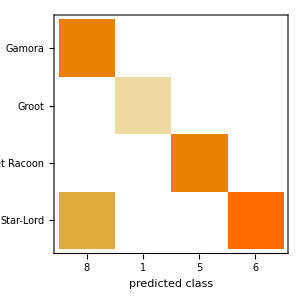

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["Examples"->{"Star-Lord","Gamora"}]
```

{-Graphics-→Star-Lord,-Graphics-→Star-Lord,-Graphics-→Star-Lord}

```mathematica
cm["WorstClassifiedExamples"->3]
```

{-Graphics-→Star-Lord,-Graphics-→Star-Lord,-Graphics-→Star-Lord}

```mathematica
cm["BestClassifiedExamples"->3]
```

{-Graphics-→Gamora,-Graphics-→Rocket Racoon,-Graphics-→Groot}

## Supervised learning: Classification

### Method selection

#### Example data

```mathematica
coloredPoints={{0.964,0.729}->RGBColor[1, 0, 0],{0.341,0.572}->RGBColor[0, 0, 1],{0.915,0.024}->RGBColor[1, 0, 0],{0.674,0.211}->RGBColor[1, 0, 0],{0.62,0.64}->RGBColor[0, 1, 0],{0.573,0.245}->RGBColor[1, 0, 0],{0.985,0.014}->RGBColor[1, 0, 0],{0.432,0.373}->RGBColor[1, 0, 0],{0.407,0.148}->RGBColor[1, 0, 0],{0.646,0.992}->RGBColor[0, 1, 0],{0.99,0.621}->RGBColor[1, 0, 0],{0.206,0.843}->RGBColor[0, 1, 0],{0.133,0.778}->RGBColor[0, 0, 1],{0.135,0.787}->RGBColor[0, 0, 1],{0.897,0.14}->RGBColor[1, 0, 0],{0.516,0.963}->RGBColor[0, 1, 0],{0.071,0.859}->RGBColor[0, 0, 1],{0.25,0.444}->RGBColor[0, 0, 1],{0.721,0.97}->RGBColor[0, 1, 0],{0.641,0.958}->RGBColor[0, 1, 0]} ;
```

```mathematica
cpc=Classify[coloredPoints,Method->Automatic]
```

```mathematica
cpc[{1,1}]
```

#### Method comparison

```mathematica
showPointClassifier[cf_]:=Graphics[Table[{PointSize[0.05],cf[{x,y}],Point[{x,y}]},{x,0,1,0.1},{y,0,1,0.1}]];
TabView[{
"Data"->Graphics[Map[Function[{datum},{PointSize[0.05],Last[datum],Point[First[datum]]}],coloredPoints]],
"NearestNeighbors"->showPointClassifier[Classify[coloredPoints,Method->"NearestNeighbors"]],
"LogisticRegression"->showPointClassifier[Classify[coloredPoints,Method->"LogisticRegression"]],
"SupportVectorMachine"->showPointClassifier[Classify[coloredPoints,Method->"SupportVectorMachine"]],
"RandomForest"->showPointClassifier[Classify[coloredPoints,Method->"RandomForest"]],
"NaiveBayes"->showPointClassifier[Classify[coloredPoints,Method->"NaiveBayes"]],
"NeuralNetwork"->showPointClassifier[Classify[coloredPoints,Method->"NeuralNetwork"]]
},ControlPlacement->Left]
```

1234567

Nearest Neighbors
Find known data points that are nearest to the target and use only those to infer the value for the input point.

Logistic regression
Fitting best linear combination of logistic sigmoid functions.

SupportVectorMachine
Find the plane that best partitions the data. Repeat with further partitoning planes.

Random forest
Construct a decision tree that repeatedly partitions the data. Do this repeatedly and chose the decision tree that gives the best predictive power.

NaiveBayes
Uses Bayes theorem assuming features are independent.

Neural Network
Multi-layered regression.

## Supervised learning: Classification

### How do you choose the method?

#### Machine learning mindset: Don’t ask “how?” or “why?” — ask “Does it work?”

#### Training vs testing data sets

```mathematica
irisData=ExampleData[{"MachineLearning","FisherIris"},"Data"]
```

```mathematica
irisTrainingData=RandomSample[irisData,100]
```

```mathematica
irisTestData=Complement[irisData,irisTrainingData]
```

```mathematica
Intersection[irisTrainingData,irisTestData]
```

```mathematica
irisCf=Classify[irisTrainingData]
```

```mathematica
irisCm=ClassifierMeasurements[irisCf,irisTestData]
```

```mathematica
irisCm["Accuracy"]
```

```mathematica
irisCm["ConfusionMatrixPlot"]
```

```mathematica
irisCm["BestClassifiedExamples"]
```

```mathematica
irisCm["Properties"]
```

#### Automating method choice

Basic optimization: Test each method on a subset of data. Choose the method that is giving the best predictions. Scale this method to all data.

## Prediction

```mathematica
data=ResourceData["Sample Data: Boston Homes"]
```

Dataset[<>]

```mathematica
ResourceData["Sample Data: Boston Homes","ColumnDescriptions"]
```

{Per capita crime rate by town,Proportion of residential land zoned for lots over 25000 square feet,Proportion of non-retail business acres per town,Charles River dummy variable (1 if tract bounds river, 0 otherwise),Nitrogen oxide concentration (parts per 10 million),Average number of rooms per dwelling,Proportion of owner-occupied units built prior to 1940,Weighted mean of distances to five Boston employment centers,Index of accessibility to radial highways,Full-value property-tax rater per $10000,Pupil-teacher ratio by town,1000(Bk-0.63)^2 where Bk is the proportion of blacks by town,Lower status of the population (percent),Median value of owner-occupied homes in $1000s}

```mathematica
data=RandomSample[data];
trainingdata=data[[;;400]];
testdata=data[[401;;]];
```

```mathematica
p=Predict[trainingdata->"MEDV", PerformanceGoal->"Quality"]
```

PredictorFunction[…]

```mathematica
pm=PredictorMeasurements[p,testdata->"MEDV" ]
```

PredictorMeasurementsObject[…]

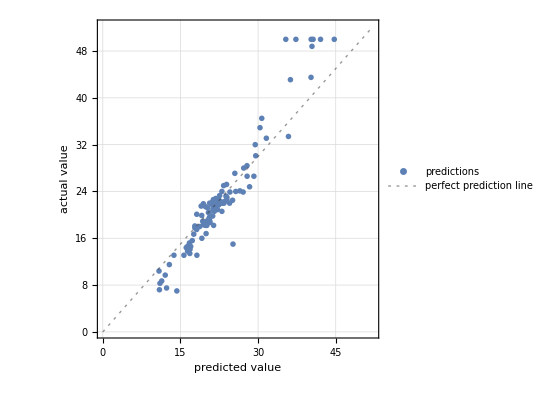

```mathematica
pm["ComparisonPlot"]
```

```mathematica
pm["Examples"->{{0,10},{10,20}}]
```

{{10.8342,0,18.1,tract does not bound Charles river,6.79×10^-7,6.782,90.8,1.8195,24,666,20.2,21.57,0.2579}→7.5,{24.8017,0,18.1,tract does not bound Charles river,6.93×10^-7,5.349,96,1.7028,24,666,20.2,396.9,0.1977}→8.3,{16.8118,0,18.1,tract does not bound Charles river,7.×10^-7,5.277,98.1,1.4261,24,666,20.2,396.9,0.3081}→7.2,{15.1772,0,18.1,tract does not bound Charles river,7.4×10^-7,6.152,100,1.9142,24,666,20.2,9.32,0.2645}→8.7,{11.5779,0,18.1,tract does not bound Charles river,7.×10^-7,5.036,97,1.77,24,666,20.2,396.9,0.2568}→9.7,{0.18337,0,27.74,tract does not bound Charles river,6.09×10^-7,5.414,98.3,1.7554,4,711,20.1,344.05,0.2397}→7}

```mathematica
pm["StandardDeviation"]
```

3.50896

```mathematica
pm["StandardDeviation","Uncertainty" -> True]
```

3.51±0.44

## Supervised learning: Prediction

### Example from images

```mathematica
trainingset=Image[AngularGauge[#]]->#&/@RandomReal[1,100];
```

```mathematica
RandomSample[trainingset,3]
```

{-Graphics-→0.818359,-Graphics-→0.19897,-Graphics-→0.481227}

```mathematica
predictor=Predict[trainingset]
```

PredictorFunction[…]

```mathematica
Row[{
AngularGauge[Dynamic[t]],
Style["→", Large],
Dynamic[Labeled[AngularGauge[predictor[Image[AngularGauge[t]]]],"(predicted value)"]]},BaseStyle->FontFamily->"Sans Serif"]
```

→

## Neural Network design

Neural networks are layers of regression that feed into each other in a way that mimics the architecture of the brain.

There is a language of primitives that you can use to build the networks.

```mathematica
?*Layer*
```

How to do this is beyond the scope of today’s session, so we will just use some pre-built networks.

## Working with neural networks

Key idea: NeuralNetworks can be represented as a symbolic graph where each layer holds fixed information about the layer type, inputs and outputs, and trainable weights. We can manipulate this expression like any other symbolic object.
Training with data just optimizes the weights in the object.

### Retraining

```mathematica
net=NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<>]

```mathematica
net[-Graphics-]
```

0

```mathematica
new=NetTrain[net,{CurrentImage[]->1}]
```

IMAQTools::grabframetimeout: Timed out acquiring image for device with ID 0

CurrentImage::grabfail: CurrentImage was unable to acquire an image.

NetTrain::encgenfail1: Could not encode training input number 1 for port "Input": $Failed was expected to be an Image or File object. Please check the example.

$Failed

## Working with neural networks

Key idea: The symbolic representation of a NeuralNetwork is just data that can be analyzed or transformed like any other data.

### Modifying and inspecting nets

```mathematica
net=NetModel["Wolfram ImageIdentify Net for WL 11.1"]
```

NetChain[<>]

```mathematica
net[-Graphics-]
```

tiger

```mathematica
Take[net,5]
```

NetChain[<>]

```mathematica
Image/@Take[net,10][-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image/@Take[net,10][-Graphics-]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Getting the best model Generalization vs overfitting

### Example: Too much freedom

```mathematica
data=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];
```

```mathematica
plot=ListPlot[List@@@data,PlotStyle->Red]
```

```mathematica
net=NetChain[{150,Tanh,150,Tanh,1},"Input"->"Scalar","Output"->"Scalar"];
net1=NetTrain[net,data,Method->"ADAM",TimeGoal->10];
```

```mathematica
Show[Plot[net1[x],{x,-3,3}],plot]
```

## Getting the best model Preventing overfitting

### Regularization

```mathematica
net2=NetTrain[net,data,Method->{"ADAM","L2Regularization"->0.001},TimeGoal->10]
```

```mathematica
Show[Plot[net2[x],{x,-3,3}],plot]
```

### ValidationSet

```mathematica
validationData=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}]
```

```mathematica
net1=NetTrain[net,data,Method->"ADAM",TimeGoal->10,ValidationSet->validationData];
```

```mathematica
Show[Plot[net1[x],{x,-3,3}],plot]
```

### DropoutLayer

```mathematica
net2=NetInsert[net,DropoutLayer[0.8],3]
```

```mathematica
net1=NetTrain[net2,data,Method->"ADAM",TimeGoal->10];
```

```mathematica
Show[Plot[net1[x],{x,-3,3}],plot]
```

# More Resources on Machine Learning

## Wolfram U Machine Learning Trainings: https://www.wolfram.com/wolfram-u/catalog/machine-learning/

## Machine Learning Super Functions: https://www.wolfram.com/language/12/high-level-machine-learning/?product=mathematica

## Wolfram Language Guide for Machine Learning: https://reference.wolfram.com/language/guide/MachineLearning.html